```mathematica
TF[model_]:=TransferFunctionModel[model,s];
Step[TFc_,t0_]:=Module[{Type,c,d,x,Gt,discreteResponse,continouseTimeResponse},
Gt=TFc[[2]];
Type =Variables[Gt][[1]];
If[Type== s,c =1,d=0];
If[Type== z,c =0,d=1];
If[c==1,x=1,x=0];
If[x==0,{discreteResponse=First@OutputResponse[TFc,UnitStep[k],{k,0,t0}],
Show[ListPlot[discreteResponse,Filling->None,PlotRange->All,DataRange->{0,t0},AxesOrigin->{0,0},Frame->True,Axes->None,Joined->True,InterpolationOrder->0,PlotStyle->{Darker[Red],Thick},GridLines->Automatic],FrameLabel->{{Style["Response y(k)",10],None},{Style["Time (sec)",10],"Step response"}},ImageSize-> Medium]}[[2]],{continouseTimeResponse=Chop@First@OutputResponse[TFc,UnitStep[t],{t,0,t0}],
Show[Plot[continouseTimeResponse,{t,0,t0},PlotRange->All,PlotStyle->{Darker[Blue],Thick},PlotRange->All,GridLines-> Automatic,Frame->True,Axes->None],FrameLabel->{{Style["Response y(t)",10],None},{Style["Time (sec)",10],"Step response"}},ImageSize-> Medium]}[[2]]]
];
```

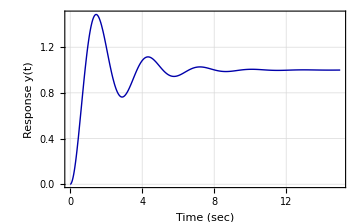

```mathematica
Gs = TF[5/(s^2+s+5)];
Step[Gs,15]
```